{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,0,0},{0,0,0,0,1},{0,1,0,1,0}}

{{1.25}}

1.25

2

{{4}}

4

4

{{5}}

5

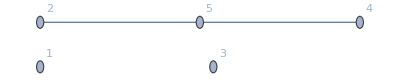

A is: {{1,2,3,4},{1,3,5}}

result is: {{1,2,3,4}}

isolated is: {5}

we are at Length[isolated]≠0

resultnew is: {{1,2,3,4}}

we are at resultnew==result

indepFromIsolated is: {{5}}

inddisjointfromIsolated is: {{5}}

we are at complete append

joined result is:{{1,2,3,4},{5}}

new isolated is: {}

we are at Length[isolated]≠0

resultfinal is: {{1,2,3,4},{5}}

Desktop/Script_Files/Matlab/D2D/ExtensionBatch/DisjointIndependentSubsets5rep7.txt

```mathematica
(* Import the connectivity matrix "D2D-connectivity-matrix.txt", generated in Matlab, in order to make the independent subsets of quantity "LI" *)
W=Import["Desktop/Script_Files/Matlab/D2D/ExtensionBatch/D2D-connectivity-matrix.txt","Table"]

(* we import the "LI", generated in Matlab, in order to make the independent subsets of size "LI" *)
LI=Import["Desktop/Script_Files/Matlab/D2D/ExtensionBatch/LI.txt","Table"]
(* we take out unnecessary {{}} of LI *)
LI=LI[[1,1]]
LI=Ceiling[LI]

(* we import the number of resources "LI", from Matlab, in order to compare the number of elements of A against the number of resources *)

resources=Import["Desktop/Script_Files/Matlab/D2D/ExtensionBatch/newD2DresourcesSRBCell1.txt","Table"]
resources=resources[[1,1]]
resources=Ceiling[resources]

(* we import the "numberOfBG", from Matlab, in order to check the presence of all BGs in the generated disjoint independent subset "result" *)
numberOfBG=Import["Desktop/Script_Files/Matlab/D2D/ExtensionBatch/numberOfBG.txt","Table"]
numberOfBG=numberOfBG[[1,1]]
BGoriginal=Range[numberOfBG];
BG=ConstantArray[0,numberOfBG];


(* to present the graph *)
W1=AdjacencyGraph[W,VertexLabels->"Name"]

(* We first find all the maximum independent subsets of size "LI" *)
A=FindIndependentVertexSet[W1,{LI,numberOfBG},All];
Print["A is: ", A]

(* The following function gets first list with removed all elements from second list which are present in first list *)
removeFrom[b_List,a_List]:=Module[{f},f[_]=0;
(f[#]=-#2)&@@@Tally[a];
Pick[b,UnitStep[f[#]++&/@b],1]];


(* The followings are all functions defined, in order to select from "A", just all the disjoint ones, in different ways; I test to see which one covers all the nodes of the graph *)
maximalDisjointSubset[list_]:=Module[{vertices=Range@Length@list,edges},edges=Cases[Subsets[vertices,2],{i_,j_}/;Intersection@@list[[{i,j}]]≠{}:>i<->j];
list[[First@FindIndependentVertexSet@Graph[vertices,edges]]]];

fn1=Module[{ms=Subsets[#,{2,Length@#}]},Take[Reverse[Pick[ms,And@@DisjointQ@@@Subsets[#,{2}]&/@ms]],UpTo[1]]]&;

fn2=Module[{ms=Subsets[#,{2,Length@#}]},Pick[ms,And@@DisjointQ@@@Subsets[#,{2}]&/@ms]]&;
(* Now we put "A" in it to generate the results *)
result=maximalDisjointSubset[A];
Print["result is: ",result]

isolated=ConstantArray[0,numberOfBG];
Do[If[FreeQ[result,i],isolated[[i]]=i],{i,1,numberOfBG}];
isolated=DeleteCases[isolated,0];
Print["isolated is: ", isolated]

(* The following function lists positions of all duplicate elements of a list. this is needed to be applied to "myvertices" list later, because we will replace all duplicate elements of it with 0, except the first occurence. then we generate "mypositions" out of it. I've no longer used this function, because I used a simpler way of doing the same thing *)
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
(*duplicates=Select[duplicates,Length[#]>1&];*)


(* In the following nested Do loop, we test if adding elements from list "isolated" to elements of "result" still keeps that element of "result" an independent subset of graph W1; If so, we add that element from "isolated" to that element of "result", otherwise we don't and we test the other element of "result", till the end *)
(* First we create a duplciate of "result" named as resultnew *)


(*
(* The big If statement *)
If[Length[result]≥resources,Print["we are at Length[result]≥resources"];result=Sort[result];extras=Length[result]- resources;If[extras≠0,Do[isolated=Append[isolated,result[[i]]],{i,1,Length[extras]}];result=Drop[result,extras];];Print["we are at resultcopy calculation"];
Do[
tempresult=result;
tempresultedges=ConstantArray[0,Length[result]];
Do[
Part[tempresult,n]=Append[Part[tempresult,n],isolated[[m]]];
Part[tempresultedges,n]=EdgeCount[Subgraph[W1,Part[tempresult,n],VertexLabels->"Name"]];
,{n,1,Length[result]}];
Print["tempresult is: ", tempresult];
Print["tempresultedges is: ", tempresultedges];
Part[result,Position[tempresultedges,Min[tempresultedges]][[1,1]]]=Part[tempresult,Position[tempresultedges,Min[tempresultedges]][[1,1]]];
,{m,1,Length[isolated]}];
resultfinal=result;Print["we just generated resultfinal"];
,Print["we are at Length[isolated]≠0"];If[Length[isolated]≠0,resultnew=result;
Do[If[IndependentVertexSetQ[W1,Append[resultnew[[j]],isolated[[i]]]],resultnew[[j]]=Append[resultnew[[j]],isolated[[i]]]],{i,1,Length[isolated]},{j,1,Length[result]}];Print["resultnew is: ", resultnew];If[resultnew==result,Print["we are at resultnew==result"];indepFromIsolated=FindIndependentVertexSet[Subgraph[W1,isolated,VertexLabels->"Name"],{1,Length[isolated]},All];
Print["indepFromIsolated is: ", indepFromIsolated];
inddisjointfromIsolated=maximalDisjointSubset[indepFromIsolated];Print["inddisjointfromIsolated is: ", inddisjointfromIsolated];If[(Length[result]+Length[inddisjointfromIsolated])≤resources,Print["we are at complete append"];result=Join[result,inddisjointfromIsolated],Print["we are at opposite to complete append"];x=resources-Length[result];temp1=Sort[inddisjointfromIsolated];Print["temp1=Sort[inddisjointfromIsolated] is: ", temp1];
OrderedinddisjointfromIsolated=Reverse[temp1];Print["reverse temp1=Sort[inddisjointfromIsolated] is: ", OrderedinddisjointfromIsolated];Do[result=Append[result,OrderedinddisjointfromIsolated[[i]]],{i,1,x}];Print["we are at result with partly appended isolated is: ", result];result=Sort[result];
result[[1]]=Append[result[[1]],Part[OrderedinddisjointfromIsolated,-(Length[OrderedinddisjointfromIsolated]-x)][[1]]];
];resultfinal=result,Do[If[MemberQ[resultnew,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];If[BG==BGoriginal,resultfinal=resultnew,result=resultnew;goneelements=Intersection[resultnew,isolated];isolated=removeFrom[isolated,goneelements];indepFromIsolated=FindIndependentVertexSet[Subgraph[W1,isolated,VertexLabels->"Name"],{1,Length[isolated]},All];
Print["indepFromIsolated is: ", indepFromIsolated];
inddisjointfromIsolated=maximalDisjointSubset[indepFromIsolated];Print["inddisjointfromIsolated is: ", inddisjointfromIsolated];If[(Length[result]+Length[inddisjointfromIsolated])≤resources,result=Append[result,inddisjointfromIsolated],x=resources-Length[result];temp1=Sort[inddisjointfromIsolated];
OrderedinddisjointfromIsolated=Reverse[temp1];Do[result=Append[result,OrderedinddisjointfromIsolated[[i]]],{i,1,x}];result=Sort[result];
result[[1]]=Append[result[[1]],Part[OrderedinddisjointfromIsolated,-(Length[OrderedinddisjointfromIsolated]-x)][[1]]];
];resultfinal=result]];,resultfinal=result]];
*)



(* Corrected the big If statement *)

Label["top"];If[Length[result]≥resources,Print["we are at Length[result]≥resources"];result=Sort[result];extras=Length[result]- resources;If[extras>0,Do[isolated=Append[isolated,result[[i]]],{i,1,Length[extras]}];result=Drop[result,extras];];Print["we are at resultcopy calculation"];
Do[
tempresult=result;
tempresultedges=ConstantArray[0,Length[result]];
Do[
Part[tempresult,n]=Append[Part[tempresult,n],isolated[[m]]];
Part[tempresultedges,n]=EdgeCount[Subgraph[W1,Part[tempresult,n],VertexLabels->"Name"]];
,{n,1,Length[result]}];
Print["tempresult is: ", tempresult];
Print["tempresultedges is: ", tempresultedges];
Part[result,Position[tempresultedges,Min[tempresultedges]][[1,1]]]=Part[tempresult,Position[tempresultedges,Min[tempresultedges]][[1,1]]];
,{m,1,Length[isolated]}];Do[If[MemberQ[result,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];
resultfinal=result;Print["we just generated resultfinal"];

,Print["we are at Length[isolated]≠0"];If[Length[isolated]≠0,resultnew=result;
Do[If[IndependentVertexSetQ[W1,Append[resultnew[[j]],isolated[[i]]]],resultnew[[j]]=Append[resultnew[[j]],isolated[[i]]]],{i,1,Length[isolated]},{j,1,Length[result]}];Print["resultnew is: ", resultnew];

If[resultnew==result,Print["we are at resultnew==result"];indepFromIsolated=FindIndependentVertexSet[Subgraph[W1,isolated,VertexLabels->"Name"],{1,Length[isolated]},All];
Print["indepFromIsolated is: ", indepFromIsolated];
inddisjointfromIsolated=maximalDisjointSubset[indepFromIsolated];Print["inddisjointfromIsolated is: ", inddisjointfromIsolated];If[(Length[result]+Length[inddisjointfromIsolated])≤resources,Print["we are at complete append"];result=Join[result,inddisjointfromIsolated];Print["joined result is:", result];,



Print["we are at opposite to complete append"];x=resources-Length[result];temp1=Sort[inddisjointfromIsolated];Print["temp1=Sort[inddisjointfromIsolated] is: ", temp1];
OrderedinddisjointfromIsolated=Reverse[temp1];Print["reverse temp1=Sort[inddisjointfromIsolated] is: ", OrderedinddisjointfromIsolated];Do[result=Append[result,OrderedinddisjointfromIsolated[[i]]],{i,1,x}];Print["we are at result with partly appended isolated is: ", result];result=Sort[result];
];

Do[If[MemberQ[result,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];      

If[BG==BGoriginal,resultfinal=result,goneelements=Intersection[Flatten[result],Flatten[isolated]];isolated=removeFrom[isolated,goneelements];Print["new isolated is: ", isolated];

Goto["top"]; 
];

,

Do[If[MemberQ[resultnew,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];If[BG==BGoriginal,resultfinal=resultnew,result=resultnew;goneelements=Intersection[Flatten[resultnew],Flatten[isolated]];isolated=removeFrom[isolated,goneelements];
indepFromIsolated=FindIndependentVertexSet[Subgraph[W1,isolated,VertexLabels->"Name"],{1,Length[isolated]},All];
Print["indepFromIsolated is: ", indepFromIsolated];
inddisjointfromIsolated=maximalDisjointSubset[indepFromIsolated];Print["inddisjointfromIsolated is: ", inddisjointfromIsolated];If[(Length[result]+Length[inddisjointfromIsolated])≤resources,result=Append[result,inddisjointfromIsolated],x=resources-Length[result];temp1=Sort[inddisjointfromIsolated];
OrderedinddisjointfromIsolated=Reverse[temp1];Do[result=Append[result,OrderedinddisjointfromIsolated[[i]]],{i,1,x}];result=Sort[result];
result[[1]]=Append[result[[1]],Part[OrderedinddisjointfromIsolated,-(Length[OrderedinddisjointfromIsolated]-x)][[1]]];
];resultfinal=result]];,resultfinal=result]];


Do[Part[resultfinal,i]=DeleteDuplicates[Part[resultfinal,i]],{i,1,Length[resultfinal]}];


Print["resultfinal is: ",resultfinal];


(* The following line exports all the independent subsets, into separate files *)
(*Do[Export["Desktop/Script_Files/Matlab/D2D/extended version2/disjointset"<>ToString[i]<>".txt",result[[i]]],{i,1,Length[result]}]*)
(* The following line exports all the independent subsets together *)
(*Export["Desktop/Script_Files/Matlab/D2D/ExtensionBatch/DisjointIndependentSubsets.txt",result]*)
Export["Desktop/Script_Files/Matlab/D2D/ExtensionBatch/DisjointIndependentSubsets5rep7.txt",resultfinal,"Table","FieldSeparators"->" "]
```

```mathematica
"Desktop/Script_Files/Matlab/D2D/ExtensionBatch/DisjointIndependentSubsets.txt"
```

Desktop/Script_Files/Matlab/D2D/ExtensionBatch/DisjointIndependentSubsets.txt